```mathematica
Clear["Global`*"]
```

### 関数

```mathematica
LoopMatrix[g_]:=(
FundLoop=FindFundamentalCycles[UndirectedGraph[g]];
RuleFundLoop=Table[EdgeRules[FundLoop[[i]]],{i,Length[FundLoop]}];
RuleRevFundLoop=Table[
EdgeRules[ReverseGraph[Graph[RuleFundLoop[[i]]]]],
{i,Length[FundLoop]}
];
Ruleg=EdgeRules[g];
Table[
Table[
If[MemberQ[RuleFundLoop[[j]],Ruleg[[i]]],1,0]+If[MemberQ[RuleRevFundLoop[[j]],Ruleg[[i]]],-1,0],
{i,EdgeCount[g]}
],
{j,Length[FundLoop]}]
)
```

```mathematica
VertexSortFromLoopEdgeList[LoopEdgeList_]:=(
UndirectedLoop=FindCycle[UndirectedGraph[LoopEdgeList]][[1]];
MinVertexNum=Min[VertexList[UndirectedLoop]];
VertexLoop={MinVertexNum};
For[j=1,Length[VertexLoop]≠ Length[UndirectedLoop],j++,
VertexLoop=Append[VertexLoop,UndirectedLoop[[FirstPosition[UndirectedLoop,VertexLoop[[j]]<->_][[1]],2]]]
];
VertexLoop=Append[VertexLoop,MinVertexNum]
)(* Vertex Sort From Loop Edge List ルールエッジで表現された巡回路から、頂点で表現された巡回路に直す *)
```

```mathematica
PartLoopByGreedyFromSort[SortList_]:=((* 入力として枝のコストの順位を与えられたときのGreedyを使った部分巡回路の構築 *)
EdgeSolution={};
EdgeProcess={Ruleg[[SortList[[1]]]]};
For[j=2,
EdgeSolution=={},
j++,
AppendEdgeProcess=Append[EdgeProcess,Ruleg[[SortList[[j]]]]];
If[Max[VertexDegree[AppendEdgeProcess]]≤2,
If[AcyclicGraphQ[UndirectedGraph[AppendEdgeProcess]],
EdgeProcess=AppendEdgeProcess,
EdgeSolution=AppendEdgeProcess
]
]
];
EdgeSolution=EdgeRules[FindCycle[UndirectedGraph[EdgeSolution]][[1]]];
VertexSortFromLoopEdgeList[EdgeSolution]
)
```

```mathematica
DelEle[list_,element_]:=list/.element->Nothing(* Delete Element *)
```

```mathematica
DelEleList[list_,elementlist_]:=list/.Table[i-> Nothing ,{i,elementlist}](* Delete Element *)
```

```mathematica
DelEdgeVertexList[edgelist_,vertexlist_]:=(
devl={};(* Variable of DelEdgeVertexList *)
Do[devl=Union[Position[edgelist,i].{{1},{0}},devl],{i,vertexlist}];
Delete[edgelist,devl]
)(* Delete Edge list from Vertex List 頂点リストから枝リストを削除（頂点リストにある頂点で構成される枝はすべて枝リストから削除）頂点リストに重複があってもUnionがあるのでOK *)
```

```mathematica
EdgeNum[Edge_]:=(
FirstPosition[EdgeRules[Gin],Edge,
FirstPosition[
EdgeRules[Gin],
EdgeRules[
ReverseGraph[{Edge}]
][[1]]
]
][[1]]
) (* Edge Number *)
```

```mathematica
EdgeNumList[Edge_]:=Table[EdgeNum[Edge[[i]]],{i,Length[Edge]}] (* Edge Number List *)
```

```mathematica
EdgeD[Edge_]:=PD[[EdgeNum[Edge]]](* Edge Distance *)
```

```mathematica
EdgeDList[Edge_]:=PD[[EdgeNumList[Edge]]](* Edge Distance *)
```

```mathematica
ListPosRef[list1_,list2_,element_]:=list1[[FirstPosition[list2,element][[1]]]](* list2でのelementの位置に来る、list1の要素を求める(list1にlist2の位置を反映 List Position Reflection) *)
```

```mathematica
EdgeReconst[Edge1_,Side1_,Edge2_,Side2_]:=VertexList[{Edge1}][[Side1]]->VertexList[{Edge2}][[Side2]](* Edge Reconstraction ２つの枝のそれぞれ片方の頂点を使って枝を再構成する *)
```

```mathematica
RestVertex[PartLoop_]:=Delete[VertexList[Gin],Table[{VertexList[PartLoop][[i]]},{i,Length[VertexList[PartLoop]]}]]
```

```mathematica
TriTourDiff[Edge_,Vertex_]:=(
EdgeD[VertexList[{Edge}][[1]]->Vertex]+EdgeD[VertexList[{Edge}][[2]]->Vertex]-EdgeD[Edge]
)(* Triangle Tour Difference *)
```

```mathematica
TriTourDiffList[PartLoop_,Vertex_]:=Table[TriTourDiff[PartLoop[[i]],Vertex],{i,Length[PartLoop]}]
```

```mathematica
MinTriTourDiffPosition[PartLoop_,Vertex_]:=(
FirstPosition[TriTourDiffList[PartLoop,Vertex],Min[TriTourDiffList[PartLoop,Vertex]]][[1]]
)
```

```mathematica
MinEdgeReconstPair[EdgePair_]:=(
ReconstEdgeD1=EdgeD[EdgeReconst[EdgePair[[1]],1,EdgePair[[2]],1]]+EdgeD[EdgeReconst[EdgePair[[1]],2,EdgePair[[2]],2]];
ReconstEdgeD2=EdgeD[EdgeReconst[EdgePair[[1]],1,EdgePair[[2]],2]]+EdgeD[EdgeReconst[EdgePair[[1]],2,EdgePair[[2]],1]];
If[
ReconstEdgeD1<ReconstEdgeD2,
{ReconstEdgeD1,{EdgeReconst[EdgePair[[1]],1,EdgePair[[2]],1],EdgeReconst[EdgePair[[1]],2,EdgePair[[2]],2]}},
{ReconstEdgeD2,{EdgeReconst[EdgePair[[1]],1,EdgePair[[2]],2],EdgeReconst[EdgePair[[1]],2,EdgePair[[2]],1]}}
]
)(* Minimum Edge Reconstraction Pair 枝ペアを再構成し、枝のコストが小さいほうのコストと枝ペアを出力 *)
```

```mathematica
SquareTourDiff[Edge1_,Edge2_]:=(
MinEdgeReconstPair[{Edge1,Edge2}][[1]]-EdgeD[Edge1]-EdgeD[Edge2]
)(* Square Tour Difference *)
```

```mathematica
SquareTourDiffList[PartLoop1_,PartLoop2_]:=Table[SquareTourDiff[i,j],{i,PartLoop1},{j,PartLoop2}]
```

```mathematica
MinSquareTourDiffEdgePair[PartLoop1_,PartLoop2_]:=(
PairNum=FirstPosition[SquareTourDiffList[PartLoop1,PartLoop2],Min[SquareTourDiffList[PartLoop1,PartLoop2]]];
{PartLoop1[[PairNum[[1]]]],PartLoop2[[PairNum[[2]]]]}
)(* 最小のスクエアツアとなるPartLoopの枝ペア *)
```

```mathematica
JoinPartLoop[PartLoop1_,PartLoop2_]:=Join[DelEleList[Join[PartLoop1,PartLoop2],MinSquareTourDiffEdgePair[PartLoop1,PartLoop2]],MinEdgeReconstPair[MinSquareTourDiffEdgePair[PartLoop1,PartLoop2]][[2]]]
```

```mathematica
PartLoopByNewUndirectedGreedyFromSort[SortList_]:=((* 枝の向きを考慮しない、入力として枝のコストの順位を与えられたときの新しいGreedyを使った部分巡回路の構築(コストは優先順位が高い順にソートされる:ランク) *)
EdgeSolution={};
For[i=3,Length[EdgeSolution]==0,i++,
EdgeSolution=FindCycle[
UndirectedGraph[EdgeList[Gout][[SortList[[Range[i]]]]]],
Infinity,All];
];
EdgeSolution=EdgeRules[EdgeSolution[[1]]];
VertexSortFromLoopEdgeList[EdgeSolution]
)
```

```mathematica
PartLoopByNewDirectedGreedyFromSort[SortList_]:=((* 枝の向きを考慮する、入力として枝のコストの順位を与えられたときの新しいGreedyを使った部分巡回路の構築(コストは優先順位が高い順にでソートされる) *)
EdgeSolution={};
For[i=3,Length[EdgeSolution]==0,i++,
EdgeSolution=FindCycle[
Graph[EdgeList[Gout][[SortList[[Range[i]]]]]],
Infinity,All];
];
EdgeSolution=EdgeRules[EdgeSolution[[1]]];
VertexSortFromLoopEdgeList[EdgeSolution]
)
```

```mathematica
RestEdgeSort[Edge_,Cost_]:=
EdgeNumList[DelEdgeVertexList[Ruleg,VertexList[Edge]]][[
Ordering[Cost[[
EdgeNumList[DelEdgeVertexList[Ruleg,VertexList[Edge]]
]]]]
]](* 残りの枝でのソート(与えられた枝をRulegから引いたエッジリストの中でのソート) *)
```

```mathematica
RestVertexMinCost[PartLoop_]:=Table[Min[TriTourDiffList[PartLoop,i]],{i,RestVertex[PartLoop]}](* 残りの頂点のそれぞれの追加コストが最小になる位置での追加コストのリスト *)
```

```mathematica
MinRestVertex[PartLoop_]:=RestVertex[PartLoop][[
FirstPosition[RestVertexMinCost[PartLoop],Min[RestVertexMinCost[PartLoop]]][[1]]
]](* 残りの頂点の中でも最小の追加コストとなる頂点 *)
```

```mathematica
LoopDelEdge[PartLoop_]:=PartLoop[[MinTriTourDiffPosition[PartLoop,MinRestVertex[PartLoop]]]](* 頂点を追加するときに削除すべき枝 *)
```

```mathematica
InsertVertexLoop[PartLoop_]:=EdgeRules[EdgeAdd[EdgeDelete[PartLoop,LoopDelEdge[PartLoop]],{VertexList[{LoopDelEdge[PartLoop]}][[1]]-> MinRestVertex[PartLoop],MinRestVertex[PartLoop]-> VertexList[{LoopDelEdge[PartLoop]}][[2]]}]](* １つの頂点を閉路に挿入したときの閉路の枝リスト *)
```

```mathematica
ContinuousInsertVertexLoop[PartLoop_]:=(
PartLoopSolution={PartLoop};
For[j=1,Min[RestVertexMinCost[PartLoopSolution[[-1]]]]≤1,
PartLoopSolution=Append[PartLoopSolution,InsertVertexLoop[PartLoopSolution[[-1]]]]
];
PartLoopSolution)(* 連続で１つの頂点を閉路に挿入したときの閉路の枝リスト *)
```

```mathematica
OutVertex[PartLoop_]:=Table[If[!RegionMember[
Polygon[Pin[[VertexSortFromLoopEdgeList[PartLoop]]]],Pin[[i]]
],i],{i,Range[Length[Pin]]}]/.Null->Nothing(* PartLoopの外側の頂点 *)
```

```mathematica
OutEdgeSortEdgeList[PartLoop_,Cost_]:=(
EdgeExceptInner=DelEdgeVertexList[Ruleg,
DelEleList[
Table[If[RegionMember[
Polygon[Pin[[VertexSortFromLoopEdgeList[PartLoop]]]],Pin[[i]]
],i],{i,Range[Length[Pin]]}]/.Null->Nothing,
VertexList[PartLoop]]
];(* PartLoopの内側の頂点を除いた頂点で構成される枝リストの変数 *)
OutEdge={};(* OutEdge is Variable *)
Do[OutEdge=Union[EdgeExceptInner[[Flatten[Position[EdgeExceptInner,i].{{1},{0}}]]],OutEdge],{i,OutVertex[PartLoop]}];
EdgeRules[Gout][[EdgeNumList[OutEdge][[Ordering[Cost[[EdgeNumList[OutEdge]]]]]]]]
)(* 部分巡回路よりも外側の頂点を見つけ、それらの頂点を含む枝のコストソートをルールエッジリストで出力 *)
```

```mathematica
InsertDetachedEdge[PartLoop_,DetachedEdge_]:=Join[DelEleList[Append[PartLoop,DetachedEdge],{MinSquareTourDiffEdgePair[PartLoop,{DetachedEdge}][[1]]}],MinEdgeReconstPair[MinSquareTourDiffEdgePair[PartLoop,{DetachedEdge}]][[2]]](* PartLoopのどの頂点にも接していない枝を挿入 *)
```

```mathematica
EdgeLoopSide[PartLoop_,ContactEdge_]:=Intersection[VertexList[PartLoop],VertexList[{ContactEdge}]][[1]](* PartLoopに接する枝のPartLoop側の頂点 *)
```

```mathematica
EdgeRestSide[PartLoop_,ContactEdge_]:=DelEle[VertexList[{ContactEdge}],EdgeLoopSide[PartLoop,ContactEdge]][[1]](* PartLoopに接する枝のPartLoop側でない頂点 *)
```

```mathematica
DelEdgeContactEdge[PartLoop_,ContactEdge_]:=PartLoop[[MinTriTourDiffPosition[PartLoop,EdgeRestSide[PartLoop,ContactEdge]]]](* PartLoopに接する枝を挿入する際に削除すべき枝 *)
```

```mathematica
InsertContactEdge[PartLoop_,ContactEdge_]:=Join[DelEle[PartLoop,DelEdgeContactEdge[PartLoop,ContactEdge]],{ContactEdge,EdgeRestSide[PartLoop,ContactEdge]->DelEle[VertexList[{DelEdgeContactEdge[PartLoop,ContactEdge]}],EdgeLoopSide[PartLoop,ContactEdge]][[1]]}](* PartLoopの頂点に接する枝を挿入 *)
```

```mathematica
InsertEdge[PartLoop_,ContactEdge_]:=If[IntersectingQ[VertexList[PartLoop],VertexList[{ContactEdge}]],InsertContactEdge[PartLoop,ContactEdge],InsertDetachedEdge[PartLoop,ContactEdge]](* PartLoopの頂点に接する枝か否かを判定し、枝を挿入 *)
```

```mathematica
EdgeNumListVertex[VertexPairList_]:=EdgeNumList[Table[i[[1]]-> i[[2]],{i,VertexPairList}]](* Edge Num List from Vertex 枝の頂点ペアのリストから枝番号のリストを出力 *)
```

```mathematica
NewDirectedGreedyFromSort[SortList_]:=((* 入力として枝のコストの順位を与えられたときのGreedyを使ったすべての頂点を含む巡回路の構築 *)
EdgeProcess={};
PartLoopVertexProcess={};(* 過程におけるすべての有効グラフの閉路の頂点リスト *)
For[j=1,
Length[PartLoopVertexProcess]≠ Length[Pin],
j++,
If[!SubsetQ[PartLoopVertexProcess,VertexList[{EdgeRules[Gout][[SortList[[j]]]]}]],
EdgeProcess=Append[EdgeProcess,EdgeRules[Gout][[SortList[[j]]]]]
];
PartLoopVertexProcess=VertexList[Flatten[PartLoopProcess=FindCycle[Graph[EdgeProcess],Infinity,All]]];
];
PartLoopProcess
)
```

```mathematica
DelEdgeNumOfRestPartLoop[EdgeListNum_,PartLoop_]:=DelEleList[EdgeListNum,DelEleList[EdgeNumListVertex[Subsets[VertexList[PartLoop],{2}]],EdgeNumList[PartLoop]]](* PartLoopを構成する枝ではないがPartLoopの頂点で構成されるすべての枝を枝リストの枝番号から削除する *)
```

```mathematica
NewDirectedGreedyFromSort2[SortList_]:=((* 入力として枝のコストの順位を与えられたときのGreedyを使ったすべての頂点を含む巡回路の構築2(枝を追加してから余分な枝を削除するアルゴリズム) *)
EdgeProcessNum={};
PartLoopVertexProcess={};(* 過程におけるすべての有効グラフの閉路の頂点リスト *)
DelEdgeProcess={};
For[j=1,Length[PartLoopVertexProcess]< Length[Pin],j++,
EdgeProcessNum=Append[EdgeProcessNum,SortList[[j]]];
PartLoopVertexProcess=VertexList[Flatten[PartLoopProcess=FindCycle[Graph[EdgeRules[Gout][[EdgeProcessNum]]],Infinity,All]]];
DelEdge={};
For[k=1,k≤Length[PartLoopProcess],k++,
tmp=EdgeProcessNum;
EdgeProcessNum=DelEdgeNumOfRestPartLoop[tmp,EdgeRules[PartLoopProcess[[k]]]];
DelEdge=Join[DelEdge,DelEleList[tmp,EdgeProcessNum]]
];
DelEdgeProcess=Append[DelEdgeProcess,DelEdge];
PartLoopVertexProcess=VertexList[Flatten[PartLoopProcess=FindCycle[Graph[EdgeRules[Gout][[EdgeProcessNum]]],Infinity,All]]]
];
PartLoopProcess
)
```

```mathematica
ComplementIntersection[List1_,List2_]:=Complement[List1∪List2,List1∩List2](* 2つのリストの共通集合の補集合を求める *)
```

```mathematica
EdgeRulesList[GraphList_]:=Table[EdgeRules[GraphList[[i]]],{i,Length[GraphList]}](* <->や->で表現されるグラフリストを枝の規則のリスト群に変換する *)
```

```mathematica
PluralPartLoopByGreedyFromRank[Rank_]:=(
PartLoopProcess={};
For[i=3,Length[PartLoopProcess]==0,i++,
PartLoopProcess=FindCycle[
Graph[EdgeList[Gout][[Rank[[Range[i]]]]]],
Infinity,All]
];
EdgeRulesList[PartLoopProcess]
)
(* 入力として枝のランクを与えられたときのGreedyの応用による複数の部分巡回路の構築 *)
```

```mathematica
DelEdgePluralPartLoop[PartLoopList_]:=(
EdgeProcessNum=EdgeNumList[Flatten[PartLoopList]];
DelEdge={};
For[k=1,k≤Length[PartLoopList],k++,
tmp=EdgeProcessNum;
EdgeProcessNum=DelEdgeNumOfRestPartLoop[tmp,PartLoopList[[k]]];
DelEdge=Join[DelEdge,DelEleList[tmp,EdgeProcessNum]]
];
EdgeRulesList[FindCycle[Graph[EdgeRules[Gout][[EdgeProcessNum]]],Infinity,All]]
)
(* Delete Edge from Plural PartLoop, 複数の部分巡回路から、PartLoopを構成する枝ではないがPartLoopの頂点で構成されるすべての枝を削除し、再度、複数の部分巡回路を見つける *)
```

```mathematica
PluralPartLoopByGreedyFromRank2[Rank_]:=(
DelEdge={};
EdgeProcess={};
PartLoopProcess={};
For[i=1,PartLoopProcess=={},i++,
AddEdge=EdgeRules[Gout][[Rank[[i]]]];
If[(PartLoopProcess=FindCycle[Graph[Append[EdgeProcess,AddEdge]],Infinity,All])=={},
If[FindCycle[UndirectedGraph[Append[EdgeProcess,AddEdge]],Infinity,All]=={},
EdgeProcess=Append[EdgeProcess,AddEdge],
DelEdge=Append[DelEdge,AddEdge];
]
]
];
EdgeRulesList[PartLoopProcess][[1]]
)
(* 入力として枝のランクを与えられたときのGreedyの応用による複数の部分巡回路の構築2(有向閉路ではないが無向閉路となるとき枝を加えない) *)
```

```mathematica
InsertVertex[PartLoop_,Vertex_]:=(
DelEdgeNum=MinTriTourDiffPosition[PartLoop,Vertex];
Join[Delete[PartLoop,DelEdgeNum],EdgeRules[Gout][[EdgeNumListVertex[{{PartLoop[[DelEdgeNum,1]],Vertex},{PartLoop[[DelEdgeNum,2]],Vertex}}]]]]
)(* 挿入したい１つの頂点を閉路に挿入したときの閉路の枝リスト *)
```

```mathematica
SortSameAs[ReferredList_,SortedList_]:=DelEleList[ReferredList,DelEleList[ReferredList,SortedList]](* 参照するリストと同じ並びでリストを並べ替える(参照するリストにない要素がある場合、その要素は出力されない) *)
```

```mathematica
MostOutEdge[PartLoop_,Rank_]:=(
OutEdgeList=DelEleList[Rank,DelEleList[Rank,EdgeNumListVertex[Tuples[{OutVertex[PartLoop],VertexList[PartLoop]}]]]];(* OutEdgeList is Variable *)
OutEdgeList[[1]]
)(* 部分巡回路よりも外側の頂点を見つけ、それらの頂点を含む枝で最もランクが高い枝を出力 *)
```

```mathematica
EdgeNumListLine[LineList_]:=EdgeNumListVertex[ToExpression[StringDelete[ToString[LineList],{"Line[","]"}]]](* Edge Num List from Line 「Line」のリストから枝番号のリストを出力 *)
```

```mathematica
EdgeRulesMesh[mesh_]:=EdgeRules[Gout][[EdgeNumListLine[MeshCells[mesh,1]]]](* Edge Rules from Mesh 「MeshRegion」のリストから枝の規則を出力 *)
```

### 渦電流の計算

```mathematica
Pin={{0,0},{1,2},{2,0.5},{3.5,3.5},{5,0}}(*Point input*)
```

{{0,0},{1,2},{2,0.5},{3.5,3.5},{5,0}}

```mathematica
Gin=DirectedGraph[CompleteGraph[Length[Pin],VertexLabels->"Name",EdgeLabels->"Name"],"Acyclic"];
```

```mathematica
Gout=Gin;
```

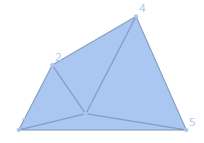

{1→2,1→3,2→3,3→5,4→5,3→4,1→5,2→4}

```mathematica
DelaunayMesh[Pin];
HighlightMesh[%,Labeled[0,"Index"]]
Ruleg=EdgeRulesMesh[%]
```

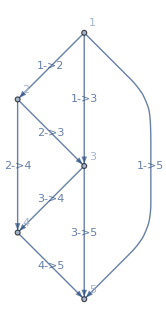

```mathematica
Gin=Graph[Ruleg,VertexLabels->"Name",EdgeLabels->"Name"](*Ggraph input*)
```

```mathematica
FundLoop=FindFundamentalCycles[UndirectedGraph[Gin]]
```

{{4<->2,2<->1,1<->5,5<->4},{4<->2,2<->1,1<->3,3<->4},{5<->1,1<->3,3<->5},{3<->1,1<->2,2<->3}}

```mathematica
RuleFundLoop=Table[EdgeRules[FundLoop[[i]]],{i,Length[FundLoop]}]
```

{{4→2,2→1,1→5,5→4},{4→2,2→1,1→3,3→4},{5→1,1→3,3→5},{3→1,1→2,2→3}}

```mathematica
RuleRevFundLoop=Table[EdgeRules[ReverseGraph[Graph[RuleFundLoop[[i]]]]],{i,Length[FundLoop]}]
```

{{4→5,2→4,1→2,5→1},{4→3,2→4,1→2,3→1},{5→3,1→5,3→1},{3→2,1→3,2→1}}

```mathematica
h=Table[
Table[
If[MemberQ[RuleFundLoop[[j]],Ruleg[[i]]],1,0]+If[MemberQ[RuleRevFundLoop[[j]],Ruleg[[i]]],-1,0],
{i,EdgeCount[Gin]}
],
{j,Length[FundLoop]}] (* 検算済 *)
```

(-1 | 0 | 0 | 0 | -1 | 0 | 1 | -1
-1 | 1 | 0 | 0 | 0 | 1 | 0 | -1
0 | 1 | 0 | 1 | 0 | 0 | -1 | 0
1 | -1 | 1 | 0 | 0 | 0 | 0 | 0)

```mathematica
PD=Table[
EuclideanDistance[
Pin[[ConnectedComponents[{EdgeRules[Gin][[i]]}][[1,1]]]],
Pin[[ConnectedComponents[{EdgeRules[Gin][[i]]}][[2,1]]]]
],
{i,Length[EdgeRules[Gin]]}];(* Point Distance *)
r=IdentityMatrix[Length[EdgeRules[Gin]]]PD;
s=Table[0,{i,Length[EdgeRules[Gin]]}];
FLP=Table[
Pin[[
ConnectedComponents[RuleFundLoop[[i]]][[1]]
]],
{i,Length[RuleFundLoop]}];(* Fundamental Loop Point *)
LoopSpin=Table[
If[(Append[FLP[[i,2]]-FLP[[i,1]],0]×Append[FLP[[i,3]]-FLP[[i,2]],0]).{0,0,1}>0,1,-1],
{i,Length[RuleFundLoop]}];(* 右回りならば負、左回りならば正 *)
FLA=Table[
Area[Polygon[
Pin[[ConnectedComponents[RuleFundLoop[[i]]][[1]]]]
]],
{i,Length[RuleFundLoop]}];(* Fundamental Loop Area *)
U=Table[LoopSpin[[i]]FLA[[i]],{i,Length[RuleFundLoop]}];(* 誘導起電力は右回りなら負、左回りなら正 *)
Curr=Transpose[h].Inverse[h.r.Transpose[h]].(h.s+U);(* 誘導起電力行列を考慮した電流を求める式 *)
```

```mathematica
Gout=Graph[Table[If[Curr[[i]]>0,
VertexList[{EdgeRules[Gin][[i]]}][[1]]->VertexList[{EdgeRules[Gin][[i]]}][[2]],
VertexList[{EdgeRules[Gin][[i]]}][[2]]->VertexList[{EdgeRules[Gin][[i]]}][[1]]
],{i,Length[EdgeRules[Gin]]}
]];(* 電流値の正負をグラフの向きに反映した出力グラフ *)
```

### TSPの解

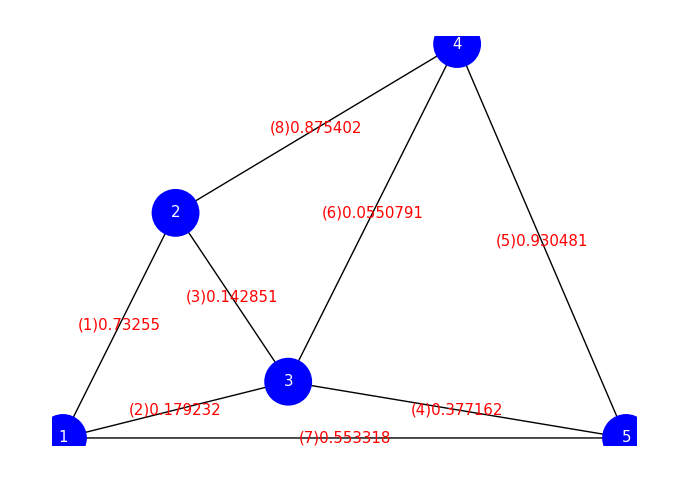

```mathematica
Graphics[{Thick,Arrowheads[{{Automatic,.8}}],Arrow[Table[
{Pin[[VertexList[{EdgeRules[Gout][[i]]}][[1]]]],Pin[[VertexList[{EdgeRules[Gout][[i]]}][[2]]]]},
{i,Length[EdgeRules[Gout]]}]],
Blue,PointSize[0.05],Point[Pin],White,Table[Text[Style[i,FontSize->15],Pin[[i]]],{i,Length[Pin]}],
Red,Table[Text[Style["("<>TextString[i]<>")"<>TextString[Abs[Curr[[i]]]],FontSize->15],(Pin[[VertexList[{EdgeRules[Gin][[i]]}][[1]]]]+Pin[[VertexList[{EdgeRules[Gin][[i]]}][[2]]]])/2],
{i,Length[EdgeRules[Gin]]}]
}](* 電流値の正負をグラフの向きに反映した出力グラフの幾何学表示 *)
```

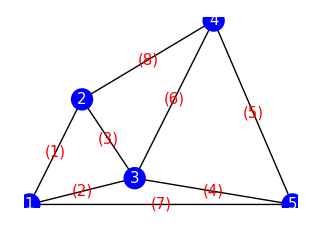

```mathematica
Graphics[{Thick,Arrowheads[{{Automatic,.8}}],Arrow[Table[
{Pin[[VertexList[{EdgeRules[Gout][[i]]}][[1]]]],Pin[[VertexList[{EdgeRules[Gout][[i]]}][[2]]]]},
{i,Length[EdgeRules[Gout]]}]],
Blue,PointSize[0.05],Point[Pin],White,Table[Text[Style[i,FontSize->15],Pin[[i]]],{i,Length[Pin]}],
Red,Table[Text[Style["("<>TextString[i]<>")",FontSize->15],(Pin[[VertexList[{EdgeRules[Gin][[i]]}][[1]]]]+Pin[[VertexList[{EdgeRules[Gin][[i]]}][[2]]]])/2],
{i,Length[EdgeRules[Gin]]}]
}](* 電流値の正負をグラフの向きに反映した出力グラフの幾何学表示 *)
```

```mathematica
Grid[{EdgeRules[Gin][[1;;10]],Range[10]},Frame->All]
Grid[{EdgeRules[Gin][[11;;20]],Range[11,20]},Frame->All]
Grid[{EdgeRules[Gin][[21;;30]],Range[21,30]},Frame->All]
Grid[{EdgeRules[Gin][[31;;40]],Range[31,40]},Frame->All]
Grid[{EdgeRules[Gin][[41;;45]],Range[41,45]},Frame->All]
```

Part::take: {1→2,1→3,2→3,3→5,4→5,3→4,1→5,2→4}の1から10の位置が取れません．

Grid[{{1→2,1→3,2→3,3→5,4→5,3→4,1→5,2→4}⟦1;;10⟧,{1,2,3,4,5,6,7,8,9,10}},Frame→All]

Part::take: {1→2,1→3,2→3,3→5,4→5,3→4,1→5,2→4}の11から20の位置が取れません．

Grid[{{1→2,1→3,2→3,3→5,4→5,3→4,1→5,2→4}⟦11;;20⟧,{11,12,13,14,15,16,17,18,19,20}},Frame→All]

Part::take: {1→2,1→3,2→3,3→5,4→5,3→4,1→5,2→4}の21から30の位置が取れません．

Grid[{{1→2,1→3,2→3,3→5,4→5,3→4,1→5,2→4}⟦21;;30⟧,{21,22,23,24,25,26,27,28,29,30}},Frame→All]

Part::take: {1→2,1→3,2→3,3→5,4→5,3→4,1→5,2→4}の31から40の位置が取れません．

Grid[{{1→2,1→3,2→3,3→5,4→5,3→4,1→5,2→4}⟦31;;40⟧,{31,32,33,34,35,36,37,38,39,40}},Frame→All]

Part::take: {1→2,1→3,2→3,3→5,4→5,3→4,1→5,2→4}の41から45の位置が取れません．

Grid[{{1→2,1→3,2→3,3→5,4→5,3→4,1→5,2→4}⟦41;;45⟧,{41,42,43,44,45}},Frame→All]

```mathematica
PDCurrCost=Abs[PD/Curr ]
```

{3.05244,11.5021,12.62,8.06385,4.09239,60.8961,9.03639,3.33044}

```mathematica
PDCurrCostSort=Ordering[PDCurrCost](* 昇順 *)
```

{1,8,5,4,7,2,3,6}

```mathematica
FindShortestTour[Pin]
Graphics[Line[Pin[[Last[%]]]]]
```

{14.0624,{1,3,5,4,2,1}}

-Graphics-

### 一貫した新しいgreedyを用いた解法4

```mathematica
PartLoop1=PluralPartLoopByGreedyFromRank2[PDCurrCostSort]
```

{2→1,1→5,5→4,4→2}

```mathematica
PartLoopProcess
```

{{2->1,1->5,5->4,4->2}}

{1,2,4,5,1}

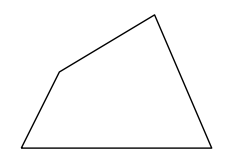

```mathematica
VertexSortFromLoopEdgeList[PartLoop1]
Graphics[line=Line[Pin[[%]]]]
```

```mathematica
PartLoop2=InsertVertex[PartLoop1,3]
```

{2→1,5→4,4→2,1→3,3→5}

{1,2,4,5,3,1}

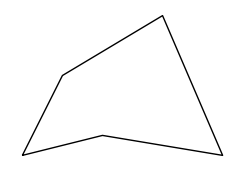

```mathematica
VertexSortFromLoopEdgeList[PartLoop2]
Graphics[line=Line[Pin[[%]]]]
```